```mathematica
Quit[]
```

### SM Early Universe with Hubble

To run simply evaluate the entire notebook SM Early Universe and look at Results

#### Documentation

The code is based upon the fact that non-thermal equilibrium corrections to the neutrino distribution functions are small. And actually, a thermal distribution function with evolving temperature ,Tν can account for the number and energy density of neutrinos very accurately. 

The result in terms of Neff in the SM is: Neff = 3.046. This is in excellent agreement with state-of-the-art calculations in the SM 1606.06986, hep-ph/0506164. In my computer the programm takes ~25 seconds to run. 

The code has 4 sections.
	1-Finite Temperature Corrections: Loads the finite temperature corrections to the electromagnetic energy and pressure densities from 1 loop QED.
	2-SM Neutrino interactions with me: Loads the SM neutrino-electron and neutrino-neutrino number and energy exchanges rates. They include the effect of the electron mass. 
	3-Thermodynamics and Expansion: Defines the relevant number, energy and pressure densities for electrons, photons and neutrinos. 
	4-Temperature ODE: Defines the time evolution equations for zγ ≡ a Tγ/m_e, and zν ≡ a Tν/m_e.
	5-Key function. Solves zγ(a) and zν(a) as well as Tγ(t) and Tν(t),

The function NeutrinoDecoupling[Tν0_] is the key one.
It outputs a vector containing: 
	1 Neff
	2 the asymtotic value of zγ
	3 the asymtotic value of zν
	4 zγ(a)
	5 zν(a)
	6 N(a)
	7 Mpl H/Tγ^2 (a), Mpl = 1.2209 10^19 10^3 MeV
	8 a(Tγ in MeV)
	9 a(t in seconds)
	10 Tγ(a)   in MeV
	11 Tγ(t in seconds) in MeV
	12 Tν/Tγ(t in seconds) 
	13 Tν/Tγ(Tγ in MeV)
	14 Mpl H/Tγ^2 (t in seconds), Mpl = 1.2209 10^19 10^3 MeV
zγ(a), zν(a)  are defined in Equation 28 of 1801.08023 and N(a) is defined in eq 60 of 1801.08023. PRIMAT uses both. 

The code is based on arXiv:1812.05605 but uses updated neutrino-neutrino and neutrino electron rates from arXiv:1907.XXXXX. All dimensionfull variables are in MeV.

#### 1-Finite Temperature Corrections

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["QED_MEV/QED_P_int.cvs","Table",HeaderLines-> 1];
Pint=Interpolation[data];
data2=Import["QED_MEV/QED_dP_intdT.cvs","Table",HeaderLines-> 1];
dPintdT:=Interpolation[data2];
data3=Import["QED_MEV/QED_d2P_intdT2.cvs","Table",HeaderLines-> 1];
d2PintdT2:=Interpolation[data3];
```

#### 2-SM Neutrino interactions with me

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Rate_MeV/nue_ann.dat","Table",HeaderLines-> 1];
fannνe=Interpolation[data];

data=Import["Rate_MeV/nue_scatt.dat","Table",HeaderLines-> 1];
fscaνe=Interpolation[data];

data=Import["Rate_MeV/numu_ann.dat","Table",HeaderLines-> 1];
fannνμ=Interpolation[data];

data=Import["Rate_MeV/numu_scatt.dat","Table",HeaderLines-> 1];
fscaνμ=Interpolation[data];

Func[T1_,T2_]:=32 0.884*(T1^9-T2^9)+56 T1^4 T2^4*0.829*(T1-T2);

ΔρSMνe[Tγ_,Tνe_,Tνμ_]:=  GF^2/π^5((1+4 SW2 +8 SW2^2)(32 0.884*fannνe[Tγ]*(Tγ^9-Tνe^9)+56 Tγ^4 *fscaνe[Tγ]*Tνe^4*0.829*(Tγ-Tνe))+2Func[Tνμ,Tνe])/.{SW2-> 0.223}/.GF-> 1.1663787 10^-11;
ΔρSMνμ[Tγ_,Tνe_,Tνμ_]:=  GF^2/π^5((1-4 SW2 +8 SW2^2)(32 0.884*fannνμ[Tγ]*(Tγ^9-Tνμ^9)+56 Tγ^4 *fscaνμ[Tγ]*Tνμ^4*0.829*(Tγ-Tνμ))-Func[Tνμ,Tνe])/.{SW2-> 0.223}/.GF-> 1.1663787 10^-11;
```

#### 3-Thermodynamics and Expansion

```mathematica
me = 0.511;
```

```mathematica
(*Number and energy densities*)
nBE[T_,μ_]:=((2 T^3)/(2 π^2))PolyLog[3,ⅇ^(-μ/T)];
nFD[T_,μ_]:=((-2 T^3)/(2 π^2)) PolyLog[3,-ⅇ^(-μ/T)];
ρBE[T_,μ_]:=((6 T^4)/(2 π^2))PolyLog[4,ⅇ^(-μ/T)];
ρFD[T_,μ_]:=((-6 T^4)/(2 π^2)) PolyLog[4,-ⅇ^(-μ/T)];

nBEM[T_,μ_,m_]:=1/(2 π^2)T^3 NIntegrate[Enred √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]-1),{Enred,m/T,∞}];
nFDM[T_,μ_,m_]:=1/(2 π^2)T^3 NIntegrate[Enred √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]+1),{Enred,m/T,∞}];
nMBM[T_,μ_,m_]:=1/(2 π^2)T^3 NIntegrate[Enred √(Enred^2-m^2/T^2)1/Exp[Enred-μ/T],{Enred,m/T,∞}];
ρBEM[T_,μ_,m_]:=1/(2 π^2)T^4 NIntegrate[Enred^2 √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]-1),{Enred,m/T,∞}];
ρFDM[T_,μ_,m_]:=1/(2 π^2)T^4 NIntegrate[Enred^2 √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]+1),{Enred,m/T,∞}];
pBEM[T_,μ_,m_]:=1/(6 π^2)T^4 NIntegrate[(Enred^2-m^2/T^2)^(3/2)1/(Exp[Enred-μ/T]-1),{Enred,m/T,∞}];
pFDM[T_,μ_,m_]:=1/(6 π^2)T^4 NIntegrate[(Enred^2-m^2/T^2)^(3/2)1/(Exp[Enred-μ/T]+1),{Enred,m/T,∞}];

dρdTFDM[T_,μ_,m_]:=1/(2 π^2)T^3 Quiet[NIntegrate[Enred^2 √(Enred^2-m^2/T^2)((Enred -μ/T) Sech[(Enred -μ/T)/2]^2)/4,{Enred,m/T,∞}]];
Partialγe[T_]:=2 (2 π^2 T^3)/15+4dρdTFDM[T,0,me]+T d2PintdT2[T] ;


Hubble[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:= √((2 ρBE[Tγ,0]+4ρFDM[Tγ,0,me]+2ρFD[Tνe,0]+4ρFD[Tνμ,μν]-Pint[Tγ]+Tγ dPintdT[Tγ]) (8 π)/(3 (1.2209 10^19 10^3)^2));


dataX=Import["Thermo_Tables/rho_FD.cvs","Table",HeaderLines-> 0];
ρFDMX=Interpolation[dataX];

HubbleTaboft[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:= 1/Tγ^2 √((2 ρBE[Tγ,0]+4 Tγ^4 ρFDMX[Tγ/me]+2ρFD[Tνe,0]+4ρFD[Tνμ,μν]-Pint[Tγ]+Tγ dPintdT[Tγ]) (8 π)/3);

HubbleTabofa[zγ_,zνe_,zνμ_,μν_,MZ_,a_]:= 1/((zγ m0)/a)^2 √((2 ρBE[(zγ m0)/a,0]+4 ((zγ m0)/a)^4 ρFDMX[((zγ m0)/a)/me]+2ρFD[(zνe m0)/a,0]+4ρFD[(zνμ m0)/a,μν]-Pint[(zγ m0)/a]+((zγ m0)/a) dPintdT[(zγ m0)/a]) (8 π)/3);

ρtot[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=(2 ρBE[Tγ,0]+4ρFDM[Tγ,0,me]+2ρFD[Tνe,0]+4ρFD[Tνμ,μν]);

ptot[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=(1/3 2 ρBE[Tγ,0]+4pFDM[Tγ,0,me]+1/3 2ρFD[Tνe,0]+4 1/3 ρFD[Tνμ,μν]);

RHSec[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=-3 Hubble[Tγ,Tνe,Tνμ,μν,MZ](ρtot[Tγ,Tνe,Tνμ,μν,MZ]+ ptot[Tγ,Tνe,Tνμ,μν,MZ]);
```

#### 4-Temperature ODE

```mathematica
FAC=1/(6.58212 10^-16 10^-6); (* Converts MeV to s^-1 *)

dTγdt[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=-FAC/Partialγe[Tγ](4 Hubble[Tγ,Tνe,Tνμ,0,0] ( 2 ρBE[Tγ,0]) +3 Hubble[Tγ,Tνe,Tνμ,0,0]*4*(ρFDM[Tγ,0,me]+pFDM[Tγ,0,me])+ ΔρSMνe[Tγ,Tνe,Tνμ]+2 ΔρSMνμ[Tγ,Tνe,Tνμ]+ 3 Hubble[Tγ,Tνe,Tνμ,0,0] Tγ dPintdT[Tγ]);


dTνdt[Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=(-Hubble[Tγ,Tνe,Tνμ,0,0] Tνe + Tνe/(3 4 2 ρFD[Tνe,0])(ΔρSMνe[Tγ,Tνe,Tνμ]+2ΔρSMνμ[Tγ,Tνe,Tνμ]))FAC;
```

```mathematica
dTνdt[10,10,2,0,0]
dTγdt[10,10,2,0,0]
```

2247.04

-3238.58

```mathematica
m0=me;

dzγda[zγ_,zνe_,zνμ_,μν_,g_,MZ_,a_]:=zγ/a(1/(zγ m0/a *Partialγe[zγ m0/a])(zγ m0/a *Partialγe[zγ m0/a]-4*2*ρBE[zγ m0/a,0]-3*4(ρFDM[zγ m0/a,0,me]+pFDM[zγ m0/a,0,me])-3*zγ m0/a dPintdT[zγ m0/a]-(ΔρSMνe[zγ m0/a,zνe m0/a,zνμ m0/a]+2 ΔρSMνμ[zγ m0/a,zνe m0/a,zνμ m0/a])/Hubble[zγ m0/a,zνe m0/a,zνμ m0/a,0,0]));

dzνeda[zγ_,zνe_,zνμ_,μν_,g_,MZ_,a_]:=zνe/a(ΔρSMνe[zγ m0/a,zνe m0/a,zνμ m0/a]/(4 Hubble[zγ m0/a,zνe m0/a,zνμ m0/a,0,0]*2*ρFDM[zνe m0/a,0,0]));

dzνμda[zγ_,zνe_,zνμ_,μν_,g_,MZ_,a_]:= zνμ/a(ΔρSMνμ[zγ m0/a,zνe m0/a,zνμ m0/a]/(4 Hubble[zγ m0/a,zνe m0/a,zνμ m0/a,0,0]*2*ρFDM[zνμ m0/a,0,0]));
```

#### 5-Key function

```mathematica
NeutrinoDecoupling[Tν0_]:=(
(*Solve first as a function of the scale factor*)
a0=m0/Tν0;amax=m0/0.01;(* Tnu ~= 0.01 MeV, a time at which e+e- have annihilated away *)

solEarlyUniverse=NDSolve[{ 
zγ'[a]==dzγda[zγ[a],zν[a],zν[a],0,0,0,a],zν'[a]==1/3(dzνeda[zγ[a],zν[a],zν[a],0,0,0,a]+2dzνμda[zγ[a],zν[a],zν[a],0,0,0,a]),
zγ[a0]==1,zν[a0]==1},{zγ,zν},{a,a0,amax},PrecisionGoal->8,AccuracyGoal->8];



(*Solve as a function of time in seconds*)
Tmin=0.01;
t0=1/(2 FAC Hubble[Tν0,Tν0,Tν0,0,0]);
tmax=1/(2 FAC Hubble[1.4 Tmin,Tmin,Tmin,0,0]);

solEarlyUniverset=NDSolve[{ 
Tγ'[t]==dTγdt[Tγ[t],Tν[t],Tν[t],0,0],Tν'[t]==dTνdt[Tγ[t],Tν[t],Tν[t],0,0],
Tγ[t0]==Tν0,Tν[t0]==Tν0},{Tγ,Tν},{t,t0,tmax},PrecisionGoal->8,AccuracyGoal->8];

(*Compute all relevant stuff*)

Neffres=(8/7(11/4)^(4/3)(4 ρFD[zν[a],0]+2 ρFD[zν[a],0])/(2ρBE[zγ[a],0])/.solEarlyUniverse/.{a-> amax})[[1]]//N;

zγofafunc[a1_]:=(zγ[a]/.solEarlyUniverse)[[1]]/.{a-> a1};

zνofafunc[a1_]:=(zν[a]/.solEarlyUniverse)[[1]]/.{a-> a1};

NaParthenope[a1_]:=((4/zγ[a]^4 7/8 π^2/15( 3 a/zν[a] D[zν[a],a]))/.solEarlyUniverse/.a-> a1)[[1]];

Hubbleofa[a1_]:=(HubbleTabofa[zγ[a]/.solEarlyUniverse,zν[a]/.solEarlyUniverse,zν[a]/.solEarlyUniverse,0,0,a1])[[1]]/.a-> a1;

Hubbleoftfunc[tt_]:=(HubbleTaboft[Tγ[t]/.solEarlyUniverset,Tν[t]/.solEarlyUniverset,Tν[t]/.solEarlyUniverset,0,0])[[1]]/.t-> tt;

Tγofafunc[a1_]:=(m0(zγ[a]/.solEarlyUniverse)[[1]])/a/.{a-> a1};

aofTγfunc[Tgam_]:=InverseFunction[Tγofafunc][Tgam];

Toftfunc[tt_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t->tt };

aoftfunc[tt_]:=aofTγfunc[Toftfunc[tt]];

Tγoftfunc[tt_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> tt};
TγTνoftfunc[tt_]:=(Tγ[t]/Tν[t]/.solEarlyUniverset)[[1]]/.{t-> tt};
TγTνofTγfunc[Tgam_]:=(zγ[a]/zν[a]/.solEarlyUniverse)[[1]]/.{a-> aofTγfunc[Tgam]};

(*1 Neff
2 the asymtotic value of zγ
3 the asymtotic value of zν
4 Interpolating function zγ(a)
5 Interpolating function zν(a)
6 Interpolating function N(a)
7 Interpolating function Mpl H/Tγ^2 (a),Mpl=1.2209 10^19 10^3 MeV
8 a(Tγ in MeV)
9 a(t in seconds)
10 Tγ(a) in MeV
11 Tγ(t in seconds) in MeV
12 Tν/Tγ(t in seconds)
13 Tν/Tγ(Tγ in MeV)
14 Mpl H/Tγ^2 (t in seconds),Mpl=1.2209 10^19 10^3 MeV*)


{Neffres,zγofafunc[amax],zνofafunc[amax],zγofafunc[a],zνofafunc[a],NaParthenope[a],Hubbleofa[a],aofTγfunc[T],aoftfunc[t],Tγofafunc[a],Tγoftfunc[t],TγTνoftfunc[t],TγTνofTγfunc[T],Hubbleoftfunc[t]});
```

#### Results

```mathematica
resultvec=Quiet[NeutrinoDecoupling[20.0]];
Print["N_eff = ", resultvec[[1]]]
Print["zγ = ", resultvec[[2]]]
Print["zν = ", resultvec[[3]]]
Print["Tγ/Tν = ", resultvec[[2]]/resultvec[[3]]]

zγofafunc[a1_]:=resultvec[[4]]/.{a-> a1};
zνofafunc[a1_]:=resultvec[[5]]/.{a-> a1};NaParthenope[a1_]:=resultvec[[6]]/.{a-> a1};Hubbleofa[a1_]:=resultvec[[7]]/.{a-> a1};aofTγfunc[Tgam_]:=resultvec[[8]]/.{T-> Tgam};aoftfunc[t1_]:=resultvec[[9]]/.{t-> t1};
Tγofafunc[a1_]:=resultvec[[10]]/.{a-> a1};
Tγoftfunc[t1_]:=resultvec[[11]]/.{t-> t1};
TγTνofTγfunc[t1_]:=resultvec[[12]]/.{t-> t1};TγTνofTγfunc[Tgam_]:=resultvec[[13]]/.{T-> Tgam};
Hubbleoft[t1_]:=resultvec[[14]]/.{t-> t1};
```

N_eff = 3.04578

zγ = 1.3978

zν = 1.00148

Tγ/Tν = 1.39573

```mathematica
Timing[zγofafunc[1]]
Timing[zνofafunc[1]]
Timing[NaParthenope[1]]
Timing[Hubbleofa[1]]
Timing[aofTγfunc[1]]
Timing[aoftfunc[1]]
Timing[Tγofafunc[1]]
Timing[Tγoftfunc[1]]
Timing[TγTνofTγfunc[1]]
Timing[TγTνofTγfunc[1]]
Timing[Hubbleoft[1]]
```

{1.13333,1.02009}

{0.000028,1.00122}

{0.000053,0.00231591}

{0.00014,5.27662}

{0.000868,0.51355}

{0.000752,0.595117}

{0.000025,0.521267}

{0.000022,0.864566}

{0.001367,1.00408}

{0.001361,1.00408}

{0.000141,5.38528}

#### Plots, some of them will get stuck. But they should run fast

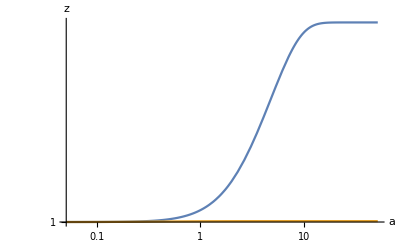

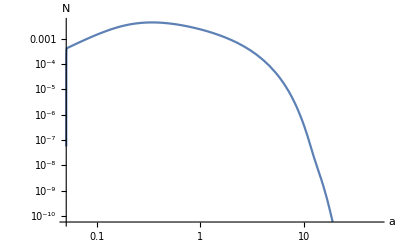

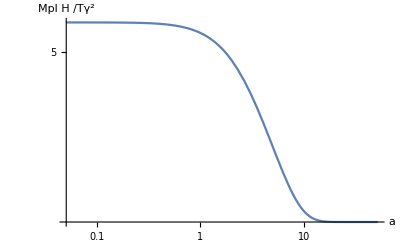

$Aborted

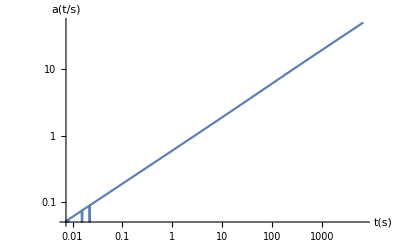

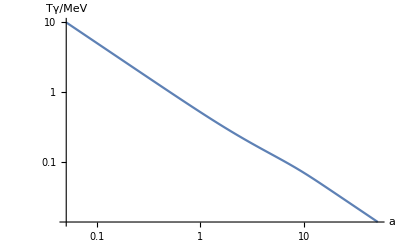

$Aborted

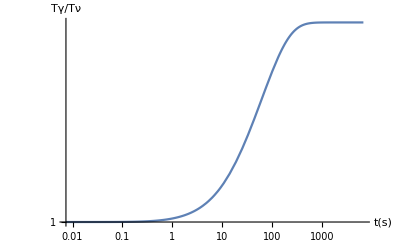

$Aborted

```mathematica
LogLogPlot[{zγofafunc[a],zνofafunc[a]},{a,a0,amax},AxesLabel->{"a","z"},PlotRange->All]

LogLogPlot[NaParthenope[a],{a,a0,amax},AxesLabel->{"a","N"}]

LogLogPlot[Hubbleofa[a],{a,a0,amax},AxesLabel->{"a","Mpl H /Tγ^2"}]

LogLogPlot[aofTγfunc[T],{T,10,0.02},AxesLabel->{"T","a(Tγ/MeV)"}]

LogLogPlot[aoftfunc[t],{t,t0,tmax},AxesLabel->{"t(s)","a(t/s)"}]

LogLogPlot[Tγofafunc[a],{a,a0,amax},AxesLabel->{"a","Tγ/MeV"}]

LogLogPlot[Tγoftfunc[t],{t,t0,tmax},AxesLabel->{"t(s)","Tγ/MeV"}]

LogLogPlot[TγTνoftfunc[t],{t,t0,tmax},AxesLabel->{"t(s)","Tγ/Tν"}]

LogLogPlot[TγTνofTγfunc[T],{T,10,0.02},AxesLabel->{"Tγ/MeV","Tγ/Tν"}]
```

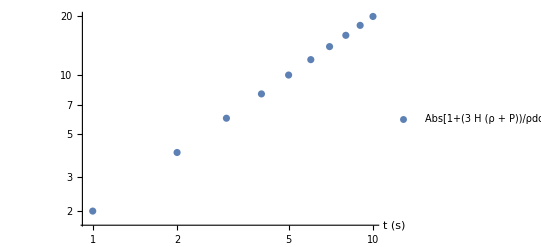

```mathematica
ListLogLogPlot[Table[{i,2i},{i,1,10}],PlotLegends->{"Abs[1+(3  H (ρ + P))/ρdot]"},AxesLabel->{"t (s)"}]
```